```mathematica
ResourceFunction["InterpolatingFunctionDomain"]
```

[◼] | InterpolatingFunctionDomain

```mathematica
MassParams=Import["/home/bell/Documents/Witek/PES/Pu240/mass2030.csv","CSV"];
```

```mathematica
MassParamsT=Transpose[MassParams];
```

```mathematica
DataB22=Table[{{MassParamsT[[1]][[i]],MassParamsT[[2]][[i]],MassParamsT[[3]][[i]]},MassParamsT[[4]][[i]]},{i,1,Length[MassParamsT[[1]]]}];
```

```mathematica
DataB33=Table[{{MassParamsT[[1]][[i]],MassParamsT[[2]][[i]],MassParamsT[[3]][[i]]},MassParamsT[[5]][[i]]},{i,1,Length[MassParamsT[[1]]]}];
```

```mathematica
DataBLL=Table[{{MassParamsT[[1]][[i]],MassParamsT[[2]][[i]],MassParamsT[[3]][[i]]},MassParamsT[[6]][[i]]},{i,1,Length[MassParamsT[[1]]]}];
```

```mathematica
DataB23=Table[{{MassParamsT[[1]][[i]],MassParamsT[[2]][[i]],MassParamsT[[3]][[i]]},MassParamsT[[7]][[i]]},{i,1,Length[MassParamsT[[1]]]}];
```

```mathematica
DataB2L=Table[{{MassParamsT[[1]][[i]],MassParamsT[[2]][[i]],MassParamsT[[3]][[i]]},MassParamsT[[8]][[i]]},{i,1,Length[MassParamsT[[1]]]}];
DataB3L=Table[{{MassParamsT[[1]][[i]],MassParamsT[[2]][[i]],MassParamsT[[3]][[i]]},MassParamsT[[9]][[i]]},{i,1,Length[MassParamsT[[1]]]}];
```

```mathematica
SurfaceInterpolB22=Interpolation[DataB22,InterpolationOrder->3];
```

```mathematica
SurfaceInterpolB33=Interpolation[DataB33,InterpolationOrder->3];
```

```mathematica
SurfaceInterpolBLL=Interpolation[DataBLL,InterpolationOrder->3];
```

```mathematica
SurfaceInterpolB23=Interpolation[DataB23,InterpolationOrder->3];
```

```mathematica
SurfaceInterpolB2L=Interpolation[DataB2L,InterpolationOrder->3];
```

```mathematica
SurfaceInterpolB3L=Interpolation[DataB3L,InterpolationOrder->3];
```

```mathematica
B220[x_,y_,z_]=SurfaceInterpolB22[x,y,z];
```

```mathematica
B330[x_,y_,z_]=SurfaceInterpolB33[x,y,z];
```

```mathematica
BLL0[x_,y_,z_]=SurfaceInterpolBLL[x,y,z];
```

```mathematica
B230[x_,y_,z_]=SurfaceInterpolB23[x,y,z];
```

```mathematica
B2L0[x_,y_,z_]=SurfaceInterpolB2L[x,y,z];
```

```mathematica
B3L0[x_,y_,z_]=SurfaceInterpolB3L[x,y,z];
```

```mathematica
PotentialValues=Import["/home/bell/Documents/Witek/PES/Pu240/pot2030.csv","CSV"];
```

```mathematica
SurfacePointsT=Transpose[PotentialValues];
```

```mathematica
DataForInterpol=Table[{{SurfacePointsT[[1]][[i]],SurfacePointsT[[2]][[i]],SurfacePointsT[[3]][[i]]},SurfacePointsT[[4]][[i]]},{i,1,Length[SurfacePointsT[[1]]]}];
```

```mathematica
SurfaceInterpol=Interpolation[DataForInterpol,InterpolationOrder->3];
```

```mathematica
Vpot0[x_,y_,z_]=SurfaceInterpol[x,y,z];
```

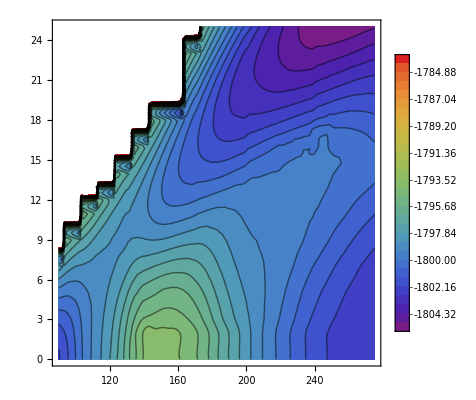

```mathematica
ContourPlot[Vpot0[x,y,0],{x,90,275},{y,0,25},Contours->30,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
(*Daniel: Here is where you import your paths*)
```

```mathematica
PathNebLine=Import["/home/bell/Documents/Witek/PES/Pu240/PathsForPlotting/NEBLine.csv"];
PathNebDP=Import["/home/bell/Documents/Witek/PES/Pu240/PathsForPlotting/NEBDP.csv"];
```

```mathematica
PathDP=Import["/home/bell/Documents/Witek/PES/Pu240/PathsForPlotting/DP.csv"];
```

```mathematica
PathPablo=Import["/home/bell/Documents/Witek/PES/Pu240/PathsForPlotting/FirstSolutionEL.csv"];
```

```mathematica
L1=0;
L2=10;
L3=20;
```

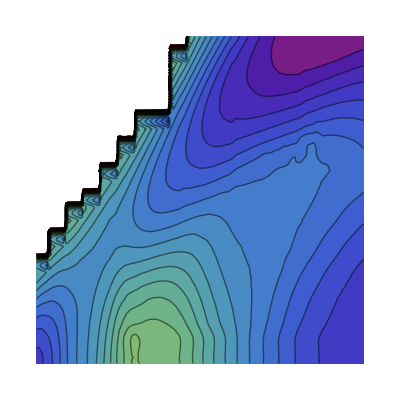

```mathematica
c1=ContourPlot[Vpot0[x,y,L1],{x,86,275},{y,0,25},Contours->30,ColorFunction->"Rainbow",Frame->False,PlotRangePadding->None,PlotLegends->None]
```

```mathematica
Show[c1,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

-Graphics-

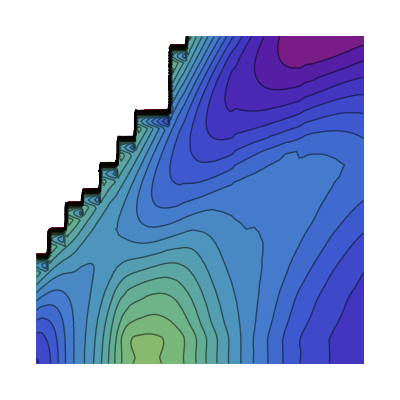

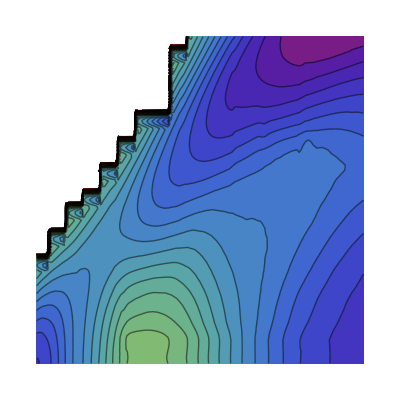

```mathematica
c2=ContourPlot[Vpot0[x,y,L2],{x,86,275},{y,0,25},Contours->30,ColorFunction->"Rainbow",Frame->False,PlotRangePadding->None,PlotLegends->None]
c3=ContourPlot[Vpot0[x,y,L3],{x,86,275},{y,0,25},Contours->30,ColorFunction->"Rainbow",Frame->False,PlotRangePadding->None,PlotLegends->None]
```

```mathematica
(*Daniel: Here you convert them to a list and then create the interpolation functions*)
```

```mathematica
PointsPathNEBLine=Table[{{i},PathNebLine[[i]]},{i,1,Length[PathNebLine]}];
```

```mathematica
PathNEBLine=Interpolation[PointsPathNEBLine];
```

```mathematica
PointsPathNEBDP=Table[{{i},PathNebDP[[i]]},{i,1,Length[PathNebDP]}];
```

```mathematica
PathNEBDP=Interpolation[PointsPathNEBDP];
```

```mathematica
PointsPathSylvester=Table[{{i},PathDP[[i]]},{i,1,Length[PathDP]}];
```

```mathematica
PathSylvester3D=Interpolation[PointsPathSylvester];
```

```mathematica
PointsELE=Table[{{i},PathPablo[[i]]},{i,1,Length[PathPablo]}];
```

```mathematica
PathELE3D=Interpolation[PointsELE];
```

```mathematica
(*Daniel: Here you make the 2D versions to have them on the bottom, they are still 3D paths whose "z" component is a constant 0.05, so they can be seen above the surface..13*)
```

```mathematica
PointsPathNEBLineProjected=Table[{{i},{PathNebLine[[i]][[1]],PathNebLine[[i]][[2]],0.05}},{i,1,Length[PathNebLine]}];
```

```mathematica
PathNEBLine2D=Interpolation[PointsPathNEBLineProjected];
```

```mathematica
PointsPathNEBDPProjected=Table[{{i},{PathNebDP[[i]][[1]],PathNebDP[[i]][[2]],0.05}},{i,1,Length[PathNebDP]}];
```

```mathematica
PathNEBDP2D=Interpolation[PointsPathNEBDPProjected];
```

```mathematica
PointsPathSylvesterProjected=Table[{{i},{PathDP[[i]][[1]],PathDP[[i]][[2]],0.1}},{i,1,Length[PathDP]}];
```

```mathematica
PathSylvester3D2D=Interpolation[PointsPathSylvesterProjected];
```

```mathematica
PointsPathELEProjected=Table[{{i},{PathPablo[[i]][[1]],PathPablo[[i]][[2]],0.1}},{i,1,Length[PathPablo]}];
```

```mathematica
PathPablo3D2D=Interpolation[PointsPathELEProjected];
```

```mathematica
Show[{Graphics3D[{Texture[c1],Polygon[{{86,0,0},{275,0,0},{275,25,0},{90,25,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"],

ParametricPlot3D[PathNEBLine[t],{t,1,Length[PathNebLine]},PlotStyle->{Magenta,Thickness[0.01],Dashed}],
ParametricPlot3D[PathNEBDP[t],{t,1,Length[PathNebDP]},PlotStyle->{Blue,Thickness[0.01],Dashed}],ParametricPlot3D[PathSylvester3D[t],{t,1,Length[PathDP]},PlotStyle->{Red,Thickness[0.01],Dashed}],
ParametricPlot3D[PathELE3D[t],{t,1,Length[PathPablo]},PlotStyle->{Orange,Thickness[0.01],Dashed}],

ParametricPlot3D[PathNEBLine2D[t],{t,1,Length[PathNebLine]},PlotStyle->{Darker[Magenta],Thickness[0.01]}],
ParametricPlot3D[PathNEBDP2D[t],{t,1,Length[PathNebDP]},PlotStyle->{Darker[Blue],Thickness[0.01]}],ParametricPlot3D[PathSylvester3D2D[t],{t,1,Length[PathDP]},PlotStyle->{Darker[Red],Thickness[0.01]}],
ParametricPlot3D[PathPablo3D2D[t],{t,1,Length[PathPablo]},PlotStyle->{Darker[Orange],Thickness[0.01]}],

ContourPlot3D[Vpot0[x,y,z]==-1802.5,{x,86,275},{y,15,25},{z,0,25},ContourStyle->{Green,Opacity[0.5]}]
},BoxRatios->{1,1,1},Axes->True,PlotRange->{{85,275},{-1,25},{0,20}},AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],LabelStyle->{18,GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Show[%77,Boxed->False]
```

-Graphics3D-